```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Table[j,{j,1,8,2}]
```

{1,3,5,7}

```mathematica
RandomInteger[{1,6},10]
```

{6,6,6,2,3,2,2,1,5,3}

```mathematica
dicerolls = RandomInteger[{1,6},10]
```

{1,5,6,2,6,5,6,2,6,2}

```mathematica
Mean[dicerolls]
```

41/10

```mathematica
1.9*Mean[dicerolls]
```

7.79

```mathematica
dicerolls=RandomInteger[{1,6},100000];
```

```mathematica
squares=Table[i^2,{i,1,8}]
```

{1,4,9,16,25,36,49,64}

```mathematica
upto8 = Range[8]
```

{1,2,3,4,5,6,7,8}

```mathematica
Map[#^2 &, upto8]
```

{1,4,9,16,25,36,49,64}

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

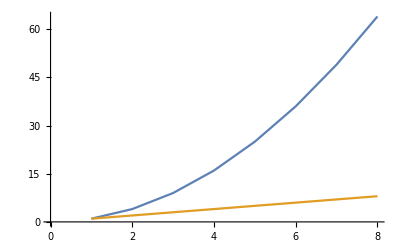

```mathematica
ListPlot[{squares,upto8},Joined->True]
```

```mathematica
Length[squares]
```

8

```mathematica
NestList[f,a,5]
```

{a,f[a],f[f[a]],f[f[f[a]]],f[f[f[f[a]]]],f[f[f[f[f[a]]]]]}